```mathematica
SIR[a_,r_,s0_,i0_,r0_,t_,n_] :=(
  x = Table[0,n+1];
 x[[1]] = s0;
y =Table[0,n + 1];
 y[[1]] = i0;
z = Table[0,n+1];
z[[1]] = r0;
h = t/n;
For[ i =1,i< n+1,i++,
  x[[i+1]] = x[[i]]*(1-h*r*y[[i]]);
y[[i+1]] = y[[i]]( 1 + h*(r*x[[i]] - a));
z[[i+1]] = z[[i]] + a*h*y[[i]];
];
{x,y,z}
)
```

```mathematica
result = SIR[0.44036,0.0017672509921504462,762,1,0,14,130];
```

```mathematica
Dimensions[result]
```

{3,131}

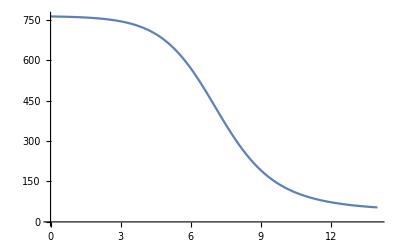

```mathematica
SEuler=ListLinePlot[Table[{(i-1)*h,result[[1]][[i]]},{i,1,Length[result[[1]]]}],PlotRange->All]
```

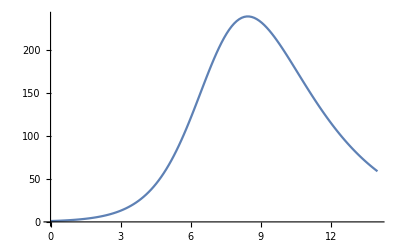

```mathematica
IEuler=ListLinePlot[Table[{(i-1)*h,result[[2]][[i]]},{i,1,Length[result[[2]]]}],PlotRange->All]
```

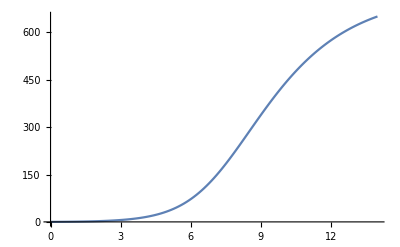

```mathematica
REuler = ListLinePlot[Table[{(i-1)*h,result[[3]][[i]]},{i,1,Length[result[[3]]]}],PlotRange->All]
```

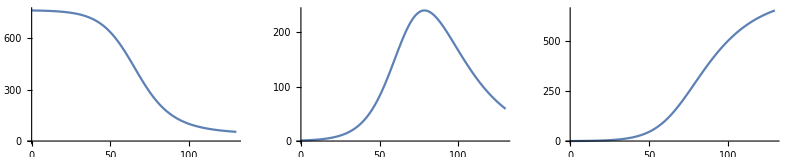

```mathematica
GraphicsRow[{ListLinePlot[Table[{i-1,result[[1]][[i]]},{i,1,Length[result[[1]]]}],PlotRange->All],ListLinePlot[Table[{i-1,result[[2]][[i]]},{i,1,Length[result[[2]]]}],PlotRange->All],ListLinePlot[Table[{i-1,result[[3]][[i]]},{i,1,Length[result[[3]]]}],PlotRange->All]}]
```

```mathematica
time={0,1,2,3,4,5,6,7,8,9,10,11,12,13};
s={{0,762},{1,750},{2,740},{3,721},{4,613},{5,332},{6,264},{7,119},{8,99},{9,78},{10,68},{11,30},{12,22},{13,0}};
i={{0,1},{1,12},{2,15},{3,29},{4,124},{5,128},{6,270},{7,252},{8,232},{9,204},{10,150},{11,96}.{12,62},{13,0}};
rmv={{0,0},{1,1},{2,8},{3,13},{4,26},{5,113},{6,161},{7,247},{8,412},{9,481},{10,545},{11,637},{12,679},{13,763}};
```

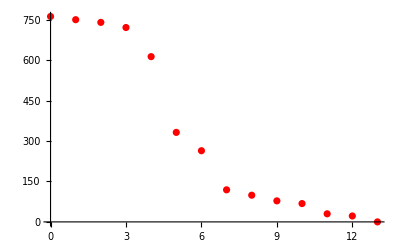

```mathematica
SReal=ListPlot[s,PlotStyle -> Red]
```

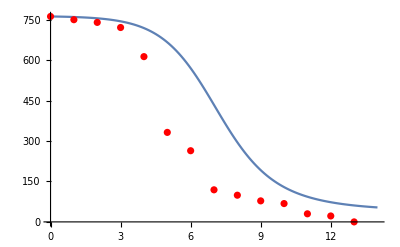

```mathematica
Show[SEuler,SReal]
```

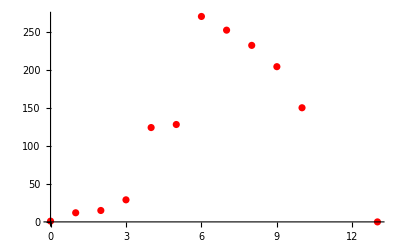

```mathematica
IReal = ListPlot[i,PlotStyle-> Red]
```

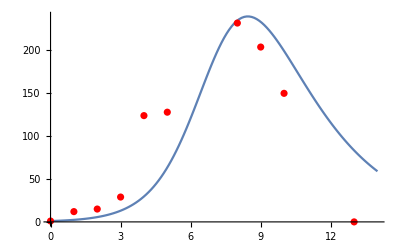

```mathematica
Show[IEuler,IReal]
```

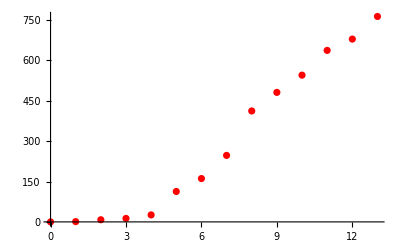

```mathematica
RReal = ListPlot[rmv,PlotStyle -> Red]
```

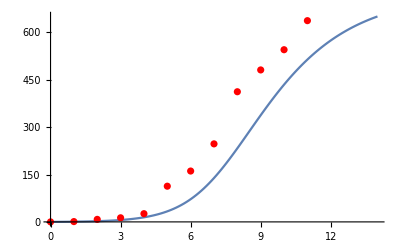

```mathematica
Show[REuler,RReal]
```